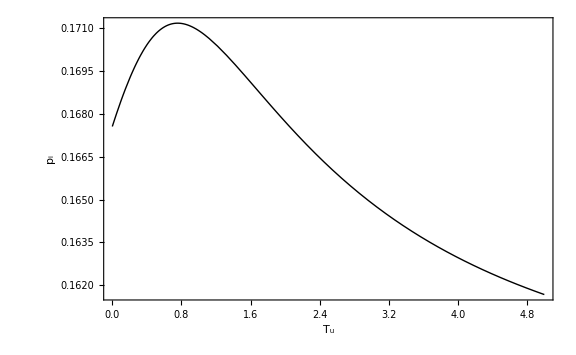

```mathematica
(*Clear*)ClearAll["Global`*"]


(*---Adjustable parameter ranges---*)paramRanges=<|"α"->{0.5,2},"γ"->{0.5,2},"γ*"->{0.5,2},"k"->{0.5,2}|>;

(*---Sample parameters---*)
seed = RandomInteger[1000];
seed = 980;

SeedRandom[seed];

params=<|"αi"->RandomReal[paramRanges["α"]],"αj"->RandomReal[paramRanges["α"]],"αk"->RandomReal[paramRanges["α"]],"γi"->RandomReal[paramRanges["γ"]],"γj"->RandomReal[paramRanges["γ"]],"γk"->RandomReal[paramRanges["γ"]],"γi*"->RandomReal[paramRanges["γ*"]],"γj*"->RandomReal[paramRanges["γ*"]],"γk*"->RandomReal[paramRanges["γ*"]],"kij"->RandomReal[paramRanges["k"]],"kik"->RandomReal[paramRanges["k"]],"kju"->RandomReal[paramRanges["k"]],"kku"->RandomReal[paramRanges["k"]]|>;

(*---Helper:p(F) from quadratic---*)
pSolve[F_,α_,γ_]:=(α-γ-F+Sqrt[(γ+F-α)^2+4 γ α])/(2 γ)

(*---Total T from p---*)
TSolve[p_,α_,γ_,γs_]:=α/γs+p (1-γ/γs)

(*---Compute p_i(Tu)---*)
piOfTu[Tu_?NumericQ]:=Module[{αi=params["αi"],αj=params["αj"],αk=params["αk"],γi=params["γi"],γj=params["γj"],γk=params["γk"],γis=params["γi*"],γjs=params["γj*"],γks=params["γk*"],kij=params["kij"],kik=params["kik"],kju=params["kju"],kku=params["kku"],pj,pk,Tj,Tk,Fi,pi},(*upstream nodes j,k*)pj=pSolve[kju Tu,αj,γj];
pk=pSolve[kku Tu,αk,γk];
Tj=TSolve[pj,αj,γj,γjs];
Tk=TSolve[pk,αk,γk,γks];
(*downstream i*)Fi=kij Tj+kik Tk;
pi=pSolve[Fi,αi,γi];
pi]

(*---Plot---*)
fontsize = 20;
fontsizePlot=24;

SetOptions[Plot,
Frame->True,
Axes->True,
AxesStyle->Directive[Black,Thickness[.003]],
FrameTicksStyle->Thickness[.003],
Method->{"AxesInFront"->False},
FrameStyle->Directive[Thickness[0.003],{FontFamily->"Arial",Black,FontSize->fontsizePlot-4}],
LabelStyle->{FontFamily->"Arial",Black,FontSize->fontsizePlot}];

Plot[piOfTu[Tu],{Tu,0,5},PlotRange->All,FrameLabel->{"T_u","p_i"},PlotStyle->Directive[Black,Thick], ImageSize->Large]
```

```mathematica
seed
```

980